## Geometrical Spreading code for homogeneous VTI media

```mathematica
Clear["Global`*"]
```

```mathematica
param={eta->0.2,t0->1,vn->2}
```

{eta→0.2,t0→1,vn→2}

## traveltime based_Shifted hyperbola:GS0

```mathematica
GS0=(t0^2 vn^2+x^2+8 eta x^2)/t0;
```

## traveltime based_Rational :GS1

```mathematica
GS1=((t0^2 vn^2+(1+2 eta) x^2)^2 (t0^4 vn^4+2 (1+eta) t0^2 vn^2 x^2+x^4))/(t0 √(t0^12 vn^12+2 (3-2 eta) t0^10 vn^10 x^2-3 (-5+2 eta+4 eta^2) t0^8 vn^8 x^4-4 (-5-4 eta+4 eta^2) t0^6 vn^6 x^6+(15+44 eta+36 eta^2-16 eta^3) t0^4 vn^4 x^8+6 (1+2 eta)^3 t0^2 vn^2 x^10+(1+2 eta)^2 (1+6 eta+4 eta^2) x^12));
```

## traveltime based_Shanks Transform

```mathematica
GS11=2/(√((t0^2 (995328 t0^38 vn^38+82944 (183+328 eta) t0^36 vn^36 x^2+13824 (7857+26280 eta+23168 eta^2) t0^34 vn^34 x^4+1152 (420471+1961712 eta+3133056 eta^2+1254400 eta^3) t0^32 vn^32 x^6-48 (-31416741-181092672 eta-390049920 eta^2-286679040 eta^3+74629120 eta^4) t0^30 vn^30 x^8+4 (869728347+5785761960 eta+14817513600 eta^2+14894392320 eta^3-3644375040 eta^4-13084524544 eta^5) t0^28 vn^28 x^10-8 (-770109039-5655435714 eta-16005265200 eta^2-19394737920 eta^3+139180032 eta^4+23512711168 eta^5+9214885888 eta^6) t0^26 vn^26 x^12+4 (2140105617+16809205455 eta+50013763848 eta^2+67734901440 eta^3+25965364224 eta^4-40496521216 eta^5-35840589824 eta^6+55289315328 eta^7) t0^24 vn^24 x^14+16 (591137352+4849583319 eta+14621211612 eta^2+20915135280 eta^3+17626175280 eta^4+14122674176 eta^5+2704293888 eta^6-10100932608 eta^7) t0^22 vn^22 x^16+4 (2092689027+17609825574 eta+52317840600 eta^2+75079254960 eta^3+95584354992 eta^4+150594974848 eta^5+82994176000 eta^6-88153128960 eta^7) t0^20 vn^20 x^18+8 (743663349+6332087520 eta+18174548880 eta^2+24724456020 eta^3+38682228720 eta^4+70287173344 eta^5+45450745856 eta^6-10110074880 eta^7) t0^18 vn^18 x^20+12 (282480939+2410875819 eta+6615843840 eta^2+7936132410 eta^3+12605610888 eta^4+23009138416 eta^5+14715944448 eta^6+7839817728 eta^7) t0^16 vn^16 x^22+12 (128268036+1091637000 eta+2868302304 eta^2+2745170160 eta^3+3160029537 eta^4+5741904272 eta^5+2210544128 eta^6+4429074432 eta^7) t0^14 vn^14 x^24+3 (183701196+1558202832 eta+3982591296 eta^2+2660529120 eta^3-461463787 eta^4+488594632 eta^5-3113577856 eta^6+514013184 eta^7) t0^12 vn^12 x^26-2 (-76518756-649768392 eta-1664521920 eta^2-690888960 eta^3+2275819137 eta^4+2457497534 eta^5+2193186528 eta^6+2020520448 eta^7) t0^10 vn^10 x^28+(32154732+275887620 eta+736676640 eta^2+231788880 eta^3-1612455255 eta^4-1793900921 eta^5-584805536 eta^6-607527936 eta^7) t0^8 vn^8 x^30+4 (1230552+10809612 eta+31313520 eta^2+14462640 eta^3-69711072 eta^4-86098075 eta^5-4745771 eta^6+12262560 eta^7) t0^6 vn^6 x^32+(516132+4714200 eta+15307488 eta^2+13448160 eta^3-20654847 eta^4-36620206 eta^5-4192743 eta^6+9583656 eta^7) t0^4 vn^4 x^34-2 (3+5 eta)^2 (-1836-11592 eta-22116 eta^2+6160 eta^3+15217 eta^4+642 eta^5) t0^2 vn^2 x^36-(3+5 eta)^2 (-108-756 eta-1980 eta^2-2300 eta^3-667 eta^4+231 eta^5) x^38))/((t0^2 vn^2+x^2)^6 (12 t0^6 vn^6+(27+104 eta) t0^4 vn^4 x^2+2 (9+14 eta) t0^2 vn^2 x^4+(3+5 eta) x^6)^5)));
```

## traveltime based_GMA_ too complicate:GS2

```mathematica
GS2=(√2)/(√((((2 x)/vn^2+(4 eta x^4 ((2 (1+8 eta+8 eta^2) x)/((1+2 eta) vn^2)+((4 (1+8 eta+8 eta^2) t0^2 x)/((1+2 eta) vn^2)+(4 x^3)/((1+2 eta)^2 vn^4))/(2 √(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))^2)-(16 eta x^3)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4))))) (-(((2 x)/vn^2+(4 eta x^4 ((2 (1+8 eta+8 eta^2) x)/((1+2 eta) vn^2)+((4 (1+8 eta+8 eta^2) t0^2 x)/((1+2 eta) vn^2)+(4 x^3)/((1+2 eta)^2 vn^4))/(2 √(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))^2)-(16 eta x^3)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))^2/(4 (t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))^(3/2)))+(2/vn^2-(8 eta x^4 ((2 (1+8 eta+8 eta^2) x)/((1+2 eta) vn^2)+((4 (1+8 eta+8 eta^2) t0^2 x)/((1+2 eta) vn^2)+(4 x^3)/((1+2 eta)^2 vn^4))/(2 √(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4))))^2)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))^3)+(4 eta x^4 ((2 (1+8 eta+8 eta^2))/((1+2 eta) vn^2)-(((4 (1+8 eta+8 eta^2) t0^2 x)/((1+2 eta) vn^2)+(4 x^3)/((1+2 eta)^2 vn^4))^2)/(4 (t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4))^(3/2))+((4 (1+8 eta+8 eta^2) t0^2)/((1+2 eta) vn^2)+(12 x^2)/((1+2 eta)^2 vn^4))/(2 √(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))^2)+(32 eta x^3 ((2 (1+8 eta+8 eta^2) x)/((1+2 eta) vn^2)+((4 (1+8 eta+8 eta^2) t0^2 x)/((1+2 eta) vn^2)+(4 x^3)/((1+2 eta)^2 vn^4))/(2 √(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))^2)-(48 eta x^2)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))/(2 √(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4))))))))/(x √(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4))))))));
```

## exact form: R3

```mathematica
q=Sqrt[(1-(1+2*eta)*p^2*vn^2)/(1-2*eta*p^2*vn^2)]/v0;
```

```mathematica
dq=Simplify[D[q,p],1-2 eta p^2 vn^2>0];
```

```mathematica
Xp=-dq*z/.z->t0*v0;
```

the expression on my own

```mathematica
R3=(t0 vn^2 √(1+4 eta p^2 vn^2-6 eta p^4 vn^4-12 eta^2 p^4 vn^4))/((1-2 eta p^2 vn^2)^2 (1-(1+2 eta) p^2 vn^2));
```

## the relative error

```mathematica
YY=x/(t0*vn)/.x->Xp;
```

```mathematica
pp1=Abs[(R3-GS0)]*100/R3/.x->Xp;
pp2=Abs[(R3-GS1)]*100/R3/.x->Xp;
pp22=Abs[(R3-GS11)]*100/R3/.x->Xp;
pp3=Abs[(R3-GS2)]*100/R3/.x->Xp;
```

```mathematica
(*{a00=ParametricPlot[{Xp/.param,pp1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,5},{0,8}},AxesLabel->{Style["x(km)",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shifted hyperbola"},Right]],
a01=ParametricPlot[{Xp/.param,pp2/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,5},{0,8}},AxesLabel->{Style["x(km)",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"rational"},Right]],a011=ParametricPlot[{Xp/.param,pp22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,5},{0,8}},AxesLabel->{Style["x(km)",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shanks transform"},Right]]};*)
```

```mathematica
{a00=ParametricPlot[{YY/.param,pp1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shifted hyperbola"},Right]],
a01=ParametricPlot[{YY/.param,pp2/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"rational"},Right]],a011=ParametricPlot[{YY/.param,pp22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shanks transform"},Right]]};
```

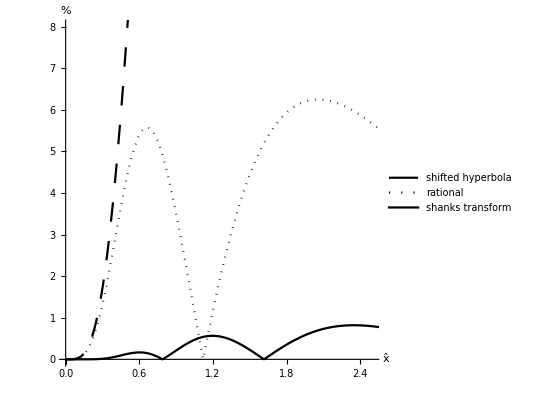

```mathematica
Show[a00,a01,a011]
```

## Direct_Shifted hyperbola:R0

```mathematica
R0=(t0 vn^2)+(((1+8 eta)^2 t0 vn^2)/(18 eta (1+4 eta)))*(Sqrt[1+((36 (eta+4 eta^2))/((1+8 eta) t0^2 vn^2))*x^2]-1);
```

## Direct_rational:R1

```mathematica
R1=Simplify[t0 vn^2+(-(-1-8 eta)/t0)*x^2+(-(9 (eta+4 eta^2))/(t0^3 vn^2))*x^4/(1+(-(9 eta (1+4 eta))/((-1-8 eta+1/(√(1+2 eta))) t0^2 vn^2))*x^2)];
```

## Direct_Shanks Transform

```mathematica
R11=t0 vn^2+x^2/t0+(eta (8 t0^2 vn^2 x^2-x^4))/(t0^3 vn^2+t0 x^2)-(9 eta^2 x^4 (-24 t0^4 vn^4+16 t0^2 vn^2 x^2+x^4)^2)/(2 t0 (t0^2 vn^2+x^2) (72 t0^8 vn^8+32 (3+22 eta) t0^6 vn^6 x^2-(27+784 eta) t0^4 vn^4 x^4-2 (27+4 eta) t0^2 vn^2 x^6-(3+5 eta) x^8));
```

## Direct_GMA:R2

```mathematica
AA0=t0 vn^2;
AA2=-(-1-8 eta)/t0;
AA4=-(9 (eta+4 eta^2))/(t0^3 vn^2);
C0=((1+6 eta) t0 vn^2)/(1/(1+2 eta))^(3/2);
C2=(√(1/(1+2 eta)))/t0;
```

```mathematica
BB2=(AA2^2-2 AA0 AA4+2 AA4 C0-2 AA2 C2+C2^2)/((AA0-C0) (AA2-C2));
BB4=(AA2-C2)^2/(AA0-C0)^2;
```

```mathematica
R2=AA0+AA2 x^2+(2 AA4 x^4)/(1+BB2 x^2+√(1+2 BB2 x^2+BB4 x^4));
```

## the relative error

```mathematica
bb1=Abs[(R3-R0)]*100/R3/.x->Xp;
bb2=Abs[(R3-R1)]*100/R3/.x->Xp;
bb22=Abs[(R3-R11)]*100/R3/.x->Xp;
bb3=Abs[(R3-R2)]*100/R3/.x->Xp;
```

```mathematica
{b00=ParametricPlot[{YY/.param,bb1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,12}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shifted hyperbola"},Right]],
b01=ParametricPlot[{YY/.param,bb2/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Small],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,12}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_rational"},Right]],b011=ParametricPlot[{YY/.param,bb22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,12}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shanks transform"},Right]]};
```

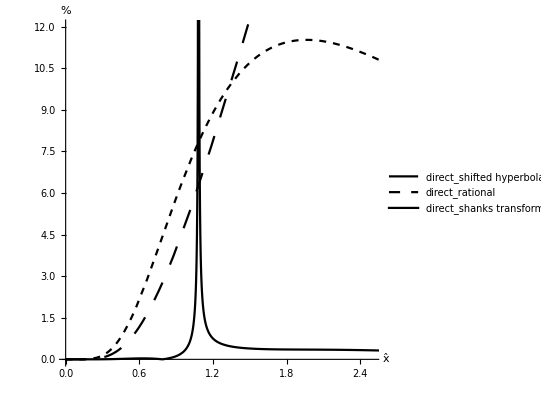

```mathematica
Show[b00,b01,b011]
```

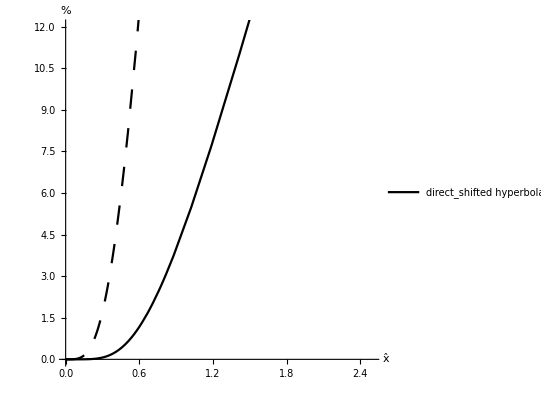
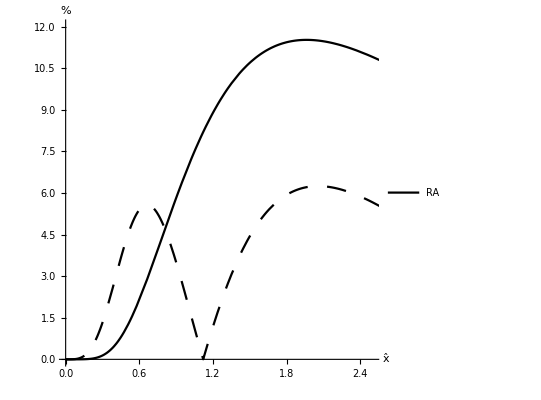
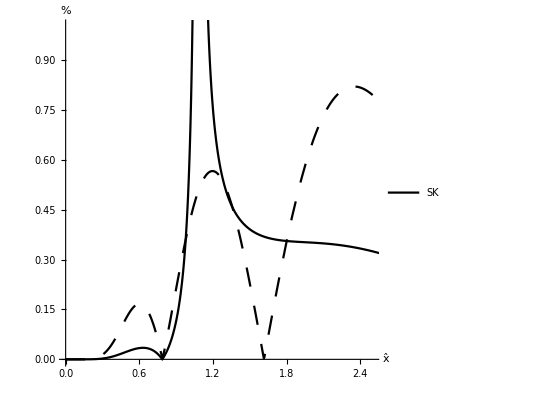

```mathematica
{ParametricPlot[{{YY/.param,bb1/.param},{YY/.param,pp1/.param}},{p,0,0.9},PlotStyle->{Directive[Black,Thick],Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,12}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"direct_shifted hyperbola"},Right]],ParametricPlot[{{YY/.param,bb2/.param},{YY/.param,pp2/.param}},{p,0,0.9},PlotStyle->{Directive[Black,Thick],Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,12}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"RA"},Right]],ParametricPlot[{{YY/.param,bb22/.param},{YY/.param,pp22/.param}},{p,0,0.9},PlotStyle->{Directive[Black,Thick],Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,1}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"SK"},Right]]}
```